# Homework 6 Section 3.5

#### 5) Plot 4 Hermite cubics

```mathematica
H0[x_] := 3*((B-x)/(B-a))^2 -(2*((B-x)/(B-a))^3)
H1[x_]:= 3*((x-a)/(B-a))^2-2*((x-a)/(B-a))^3
S0[x_] := ((B-x)^2/(B-a)) - ((B-x)^3/(B-a)^2)
S1[x_] := -((x-a)^2/(B-a)) + ((x-a)^3/(B-a)^2)
```

```mathematica
a= -10;
B=10;
```

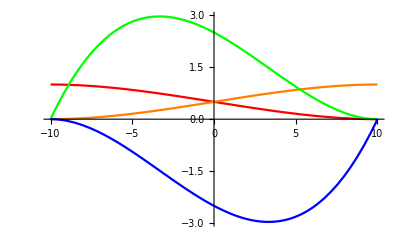

```mathematica
Plot[{H0[x],H1[x],S0[x], S1[x]},{x,a,B}, PlotStyle->{Red,Orange,Green,Blue}]
```

This satisfies definition 3.5.1 because H0(a) = 1, H0(B) = 0 and both derivatives of H0 at the end points are zero.The green and blue curve are the derivates and it shows that the value is 0 when it hits x = 10 and x = -10. I used the interval [-10,10] as an arbitrary interval to view the graph clearly. H0 and H1 are even functions, so they are merely reflections of each other across the y-axis. We can see that S0 and S1 vanishes at its end points and the derivative of H0 and H1 also vanishes at its end points.